# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=1.99999;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31401,2}

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,generateCoherentStateCompiler,generateSpinOperators}

```mathematica
(*Floquet parameters*)
J=500;
d=2 J+1;
α=0.84;
τ=1.0;
k=11.85;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 31401 points...

```mathematica
?Floq
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

Computing Floquet matrix...

```mathematica
sz=ops[[3]];
(*Compute expected values of Sz for each eigenvector*)
szExpectations=Map[#.sz.ConjugateTranspose[#]&,neweigenvec];
(*Get ordering of eigenvectors by increasing<Sz>*)
ordering=Ordering[szExpectations];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprCompiled}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
husimiValues=Abs[overlaps]^2;
```

```mathematica
q=1;
husimis=Table[husimiValues[[q]]^2,{q,2J+1}];
```

```mathematica
plots=ListDensityPlot[MapThread[Append,{region,Total[husimis[[1;;500]]]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q ="<>ToString[q],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
plots=ListDensityPlot[MapThread[Append,{region,Total[husimis[[1;;500]]]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q ="<>ToString[q],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
(*Set parameters*)
numEigenstates=2J+1; 
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,2J+1}];
```

$Aborted

```mathematica
(*Partial husimis*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,Total[husimis[[1;;q]]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,2,2J+1}];
```

## Sorting with shannon entropy

```mathematica
Clear[entropy];
entropy[0|0.]=0;
entropy[x_]:=-x*Log[x];
```

```mathematica
shannon=Table[Total[Map[entropy,i]] ,{i,Abs[neweigenvec]^2}];
info=SortBy[Transpose[{Chop[shannon],neweigenvec}],First];
eigenvecsSorted=info[[All,2]];
```

# Localization measures

```mathematica
J=500;
```

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

```mathematica
Clear[mat];
mat=Floq[J,α,k,τ];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
iprCompiled=Total[Abs[overlaps]^4,{1}];
husimiValues=Abs[overlaps]^2;
```

```mathematica
(*region={{Q1,P1},{Q2,P2},...} are your grid points inside r<=2*)
weights=ConstantArray[4*Pi/Length[region],Length[region]];
pref=(2J+1)/(4*Pi);
```

```mathematica
eps=$MachineEpsilon;
Clear[SWehrl];
SWehrl[k_Integer]:=Module[{Q=husimiValues[[k]]},-pref*Total[weights*Q*Log[Clip[Q,{eps,Infinity}]]]];
```

```mathematica
Clear[SWehrlFromRow];
SWehrlFromRow[Qrow_List]:=Module[{Z=Total[weights*Qrow],Qn},Qn=Qrow/Z;
-pref*Total[weights*Qn*Log[Clip[Qn,{$MachineEpsilon,∞}]]]];
```

```mathematica
normChecks=ParallelTable[pref*Total[weights*i],{i,husimiValues}];
```

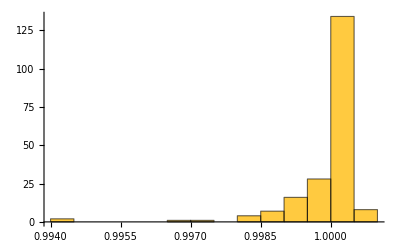

```mathematica
Histogram[normChecks,PlotRange->All]
```

```mathematica
entropies=ParallelMap[SWehrlFromRow,husimiValues];
```

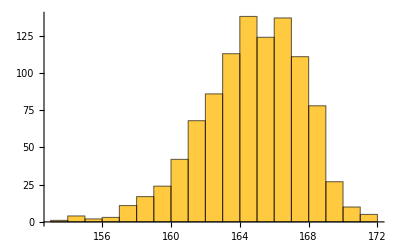

```mathematica
Histogram[entropies,PlotRange->All]
```

```mathematica
perm=Ordering[entropies];
entropiesSorted=entropies[[perm]];
eigenvecsSorted=neweigenvec[[perm]];
overlapsSorted=overlaps[[perm,All]];
husimiValuesSorted=husimiValues[[perm]];
```